```mathematica
CIEvalues={{0.0014,0.0000,0.0065},{0.0022,0.0001,0.0105},{0.0042,0.0001,0.0201},{0.0076,0.0002,0.0362},{0.0143,0.0004,0.0679},{0.0232,0.0006,0.1102},{0.0435,0.0012,0.2074},{0.0776,0.0022,0.3713},{0.1344,0.0040,0.6456},{0.2148,0.0073,1.0391},{0.2839,0.0116,1.3856},{0.3285,0.0168,1.6230},{0.3483,0.0230,1.7471},{0.3481,0.0298,1.7826},{0.3362,0.0380,1.7721},{0.3187,0.0480,1.7441},{0.2908,0.0600,1.6692},{0.2511,0.0739,1.5281},{0.1954,0.0910,1.2876},{0.1421,0.1126,1.0419},{0.0956,0.1390,0.8130},{0.0580,0.1693,0.6162},{0.0320,0.2080,0.4652},{0.0147,0.2586,0.3533},{0.0049,0.3230,0.2720},{0.0024,0.4073,0.2123},{0.0093,0.5030,0.1582},{0.0291,0.6082,0.1117},{0.0633,0.7100,0.0782},{0.1096,0.7932,0.0573},{0.1655,0.8620,0.0422},{0.2257,0.9149,0.0298},{0.2904,0.9540,0.0203},{0.3597,0.9803,0.0134},{0.4334,0.9950,0.0087},{0.5121,1.0000,0.0057},{0.5945,0.9950,0.0039},{0.6784,0.9786,0.0027},{0.7621,0.9520,0.0021},{0.8425,0.9154,0.0018},{0.9163,0.8700,0.0017},{0.9786,0.8163,0.0014},{1.0263,0.7570,0.0011},{1.0567,0.6949,0.0010},{1.0622,0.6310,0.0008},{1.0456,0.5668,0.0006},{1.0026,0.5030,0.0003},{0.9384,0.4412,0.0002},{0.8544,0.3810,0.0002},{0.7514,0.3210,0.0001},{0.6424,0.2650,0.0000},{0.5419,0.2170,0.0000},{0.4479,0.1750,0.0000},{0.3608,0.1382,0.0000},{0.2835,0.1070,0.0000},{0.2187,0.0816,0.0000},{0.1649,0.0610,0.0000},{0.1212,0.0446,0.0000},{0.0874,0.0320,0.0000},{0.0636,0.0232,0.0000},{0.0468,0.0170,0.0000},{0.0329,0.0119,0.0000},{0.0227,0.0082,0.0000},{0.0158,0.0057,0.0000},{0.0114,0.0041,0.0000},{0.0081,0.0029,0.0000},{0.0058,0.0021,0.0000},{0.0041,0.0015,0.0000},{0.0029,0.0010,0.0000},{0.0020,0.0007,0.0000},{0.0014,0.0005,0.0000},{0.0010,0.0004,0.0000},{0.0007,0.0002,0.0000},{0.0005,0.0002,0.0000},{0.0003,0.0001,0.0000},{0.0002,0.0001,0.0000},{0.0002,0.0001,0.0000},{0.0001,0.0000,0.0000},{0.0001,0.0000,0.0000},{0.0001,0.0000,0.0000},{0.0000,0.0000,0.0000}};
```

```mathematica
xrvalues=Table[{i 5+380,CIEvalues[[i+1]][[1]]},{i,0,80}];
xgvalues=Table[{i 5+380,CIEvalues[[i+1]][[2]]},{i,0,80}];
xbvalues=Table[{i 5+380,CIEvalues[[i+1]][[3]]},{i,0,80}];
```

```mathematica
xr=Interpolation[xrvalues];
xg=Interpolation[xgvalues];
xb=Interpolation[xbvalues];
```

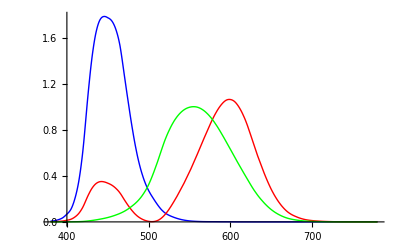

```mathematica
Plot[{xb[l],xr[l],xg[l]},{l,380,780},PlotStyle->{Blue,Red,Green}]
```

```mathematica
1/Integrate[xr[l],{l,380,780}]
1/Integrate[xb[l],{l,380,780}]
1/Integrate[xg[l],{l,380,780}]
```

0.00935859

0.00935962

0.00935842

```mathematica
cr=0.009358589566966362;
cb=0.009359620607778663;
cg=0.009358423526764798;
```

```mathematica
p[l_]:=If[390<l<450, 1, 0]
```

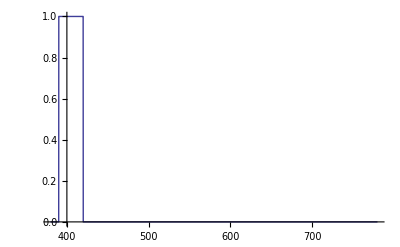

```mathematica
Plot[p[l] , {l,380,780}]
```

```mathematica
SMPTE={{0.630, 0.310,0.155},{0.340,0.595,0.070},{1-0.630-0.34,1-.31-.595,1-.155-0.07}}
```

{{0.63,0.31,0.155},{0.34,0.595,0.07},{0.03,0.095,0.775}}

```mathematica
RGB={{3.240497, -1.537150, -0.498535},{-0.969256, 1.875992,0.041556},{0.055648, -0.204043,1.057311}};
RGB//MatrixForm
```

(3.2405 | -1.53715 | -0.498535
-0.969256 | 1.87599 | 0.041556
0.055648 | -0.204043 | 1.05731)

{-17.8722,57.3498,-5.69195}

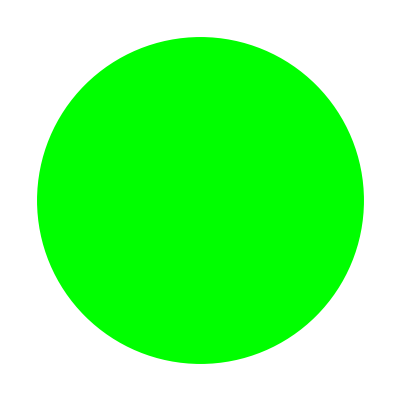

```mathematica
p[l_]:=If[520<l<560, 1, 0]
x=Integrate[ p[l] xr[l],{l,380,780}];
y=Integrate[ p[l] xg[l],{l,380,780}];
z=Integrate[ p[l] xb[l],{l,380,780}];
RGB.{x,y,z}
Graphics[{RGBColor[RGB.{x,y,z}],Disk[]}]
```

```mathematica
Colour of the sun
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.27947×10^-29 and 7.50678×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.98697×10^-29 and 6.93571×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.27947×10^-29 and 7.50678×10^-35 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

{0.567678,0.327883,0.202313}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.27947×10^-29 and 7.50678×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.98697×10^-29 and 6.93571×10^-35 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.27947×10^-29 and 7.50678×10^-35 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

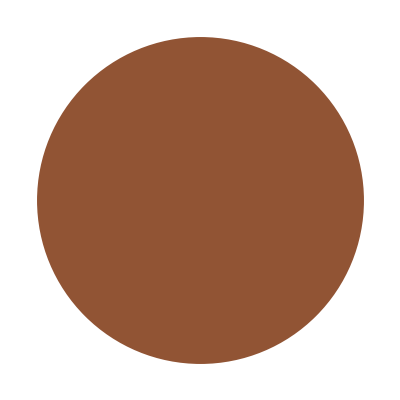

```mathematica
h=6.626 10^-34;
c=299700000;
T=5778;
k=1.380 10^-23;
p[l_]:=2h l^3/c^2  (1/(E^(h l/(k T))-1));
X=Integrate[ p[l] xr[l],{l,380,780}];
Y=Integrate[ p[l] xg[l],{l,380,780}];
Z=Integrate[ p[l] xb[l],{l,380,780}];
x=X/(X+Y+Z);
y=Y/(X+Y+Z);
z=Z/(X+Y+Z);
RGB.{x,y,z}
Graphics[{RGBColor[RGB.{x,y,z}],Disk[]}]
```

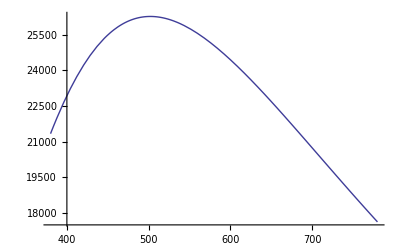

{0.373715,0.327594,0.306522}

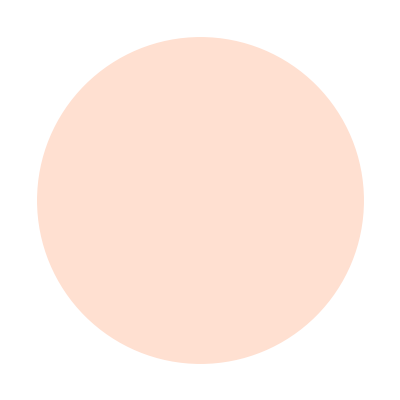

```mathematica
h=6.626 10^-34 10^18;
c=3 10^8 10^9;
T=5778;
k=1.380 10^-23 10^18;
sun[l_]:=2h c^2/l^5  (1/(E^(h c/(l k T))-1));
Plot[sun[l],{l,380,780}]
X=680Sum[ sun[l] xr[l],{l,380,780,5}];
Y=680 Sum[ sun[l] xg[l],{l,380,780,5}];
Z=680 Sum[ sun[l] xb[l],{l,380,780,5}];
x=X/(X+Y+Z);
y=Y/(X+Y+Z);
z=Z/(X+Y+Z);
RGB.{x,y,z}
Graphics[{RGBColor[1/0.37371537470152233 RGB.{x,y,z}],Disk[]}]
```

```mathematica
RGB.{x,y,z}/10 255
```

{167.058,162.614,181.679}

```mathematica
Human colour perception correction
```

```mathematica
395 1.05965 10^-03
```

0.418562

```mathematica
data={{380,4.14616  10^-4},{385,4.14616  10^-4},{390 , 4.14616  10^-4},{
395 , 1.05965  10^-3},{
400 , 2.45219  10^-3},{
405 , 4.97172  10^-3},{
410 , 9.07986  10^-3},{
415 , 1.42938  10^-2},{
420 , 2.02737  10^-2},{
425 , 2.61211  10^-2},{
430 , 3.31904  10^-2},{
435 , 4.15794  10^-2},{
440 , 5.03366  10^-2},{
445 , 5.74339  10^-2},{
450 , 6.47235  10^-2},{
455 , 7.23834  10^-2},{
460 , 8.51482  10^-2},{
465 , 1.06014  10^-1},{
470 , 1.29896  10^-1},{
475 , 1.53507  10^-1},{
480 , 1.78805  10^-1},{
485 , 2.06483  10^-1},{
490 , 2.37916  10^-1},{
495 , 2.85068  10^-1},{
500 , 3.48354  10^-1},{
505 , 4.27760  10^-1},{
510 , 5.20497  10^-1},{
515 , 6.20626  10^-1},{
520 , 7.18089  10^-1},{
525 , 7.94645  10^-1},{
530 , 8.57580  10^-1},{
535 , 9.07135  10^-1},{
540 , 9.54468  10^-1},{
545 , 9.81411  10^-1},{
550 , 9.89023  10^-1},{
555 , 9.99461  10^-1},{
560 , 9.96774  10^-1},{
565 , 9.90255  10^-1},{
570 , 9.73261  10^-1},{
575 , 9.42457  10^-1},{
580 , 8.96361  10^-1},{
585 , 8.58720  10^-1},{
590 , 8.11587  10^-1},{
595 , 7.54479  10^-1},{
600 , 6.91855  10^-1},{
605 , 6.27007  10^-1},{
610 , 5.58375  10^-1},{
615 , 4.89595  10^-1},{
620 , 4.22990  10^-1},{
625 , 3.60924  10^-1},{
630 , 2.98086  10^-1},{
635 , 2.41690  10^-1},{
640 , 1.94312  10^-1},{
645 , 1.54740  10^-1},{
650 , 1.19312  10^-1},{
655 , 8.97959  10^-2},{
660 , 6.67104  10^-2},{
665 , 4.89970  10^-2},{
670 , 3.55998  10^-2},{
675 , 2.55422  10^-2},{
680 , 1.80794  10^-2},{
685 , 1.26157  10^-2},{
690 , 8.66128  10^-3},{
695 , 6.02768  10^-3},{
700 , 4.19594  10^-3},{
705 , 2.91086  10^-3},{
710 , 1.99556  10^-3},{
715 , 1.36702  10^-3},{
720 , 9.44727  10^-4},{
725 , 6.53705  10^-4},{
730 , 4.55597  10^-4},{
735 , 3.17974  10^-4},{
740 , 2.21745  10^-4},{
745 , 1.56557  10^-4},{
750 , 1.10393  10^-4},{
755 , 7.82744  10^-5},{
760 , 5.57886  10^-5},{
765 , 3.98188  10^-5},{
770 , 2.86018  10^-5},{
775 , 2.05126  10^-5},{
780 , 1.48724  10^-5},{
785 , 1.08000  10^-5},{
790 , 7.86392  10^-6},{
795 , 5.73694  10^-6},{
800 , 4.21160  10^-6},{
805 , 3.10656  10^-6},{
810 , 2.28679  10^-6},{
815 , 1.69315  10^-6},{
820 , 1.26256  10^-6},{
825 , 9.42251  10^-7},{
830 , 7.05386  10^-7},
{835,0},{840,0},{845,0},{850,0}};
```

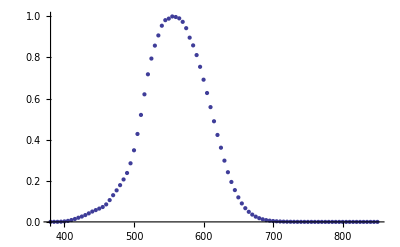

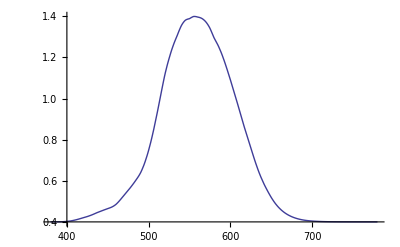

```mathematica
ListPlot[data]
Sensitivity=Interpolation[data];
Plot[Sensitivity[x]+0.4,{x,380,780}]
```

{3.42628×10^7,-6.86283×10^6,6.9652×10^7}

{0.491915,-0.0985304,1.}

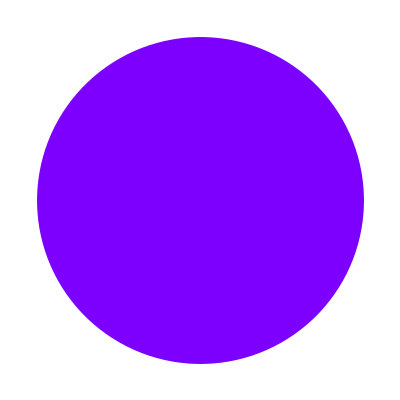

```mathematica
po[l_]:=If[0<l<800, 1, 0];
p[l_]:=sun[l]/(Sensitivity[l])
x=Integrate[ p[l] xr[l],{l,380,780}];
y=Integrate[ p[l] xg[l],{l,380,780}];
z=Integrate[ p[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

```mathematica
Rayleigh scattering
```

```mathematica
S[t_,l_]:=1/l^4 (1+Cos[t]^2)
```

```mathematica
t=Pi/4;
x=Sum[ S[l] cr xr[l],{l,380,780}];
y=Sum[ S[l] cg xg[l],{l,380,780}];
z=Sum[ S[l] cb xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{-0.498535 (0.+0.0000608375 S[380]+0.0000645365 S[381]+0.0000700624 S[382]+«255»)-1.53715 («1»)+3.2405 (0.+0.000013102 S[380]+«398»+3.06962×10^-7 S[779]),«1»,«1»}

{(-0.498535 (0.+0.0000608375 S[380]+«257»)-«1»+3.2405 (0.+«399»+3.06962×10^-7 S[779]))/Max[0.041556 (0.+0.0000608375 S[380]+«257»)+1.87599 («1»)-0.969256 («1»),«1»,«1»],(«1»)/(«1»),(«1»)/Max[«1»]}

-Graphics-

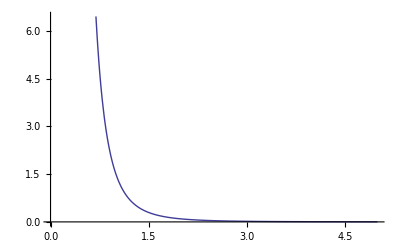

```mathematica
Plot[1/l^4 (1+Cos[t]^2),{l,0,5}]
```

```mathematica
Let's try again
```

```mathematica
S[l_]:=b/(l+a) ^4
a
b
```

a

b

```mathematica
Solve[{b/a^4==.25,b/(a+650)^4==.05},{a,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→-260.485,b→1.15098×10^9},{a→-200.861-300.357 ⅈ,b→-3.01798×10^9-3.00862×10^9 ⅈ},{a→-200.861+300.357 ⅈ,b→-3.01798×10^9+3.00862×10^9 ⅈ},{a→1312.21,b→7.41223×10^11}}

1312

7.41223×10^11

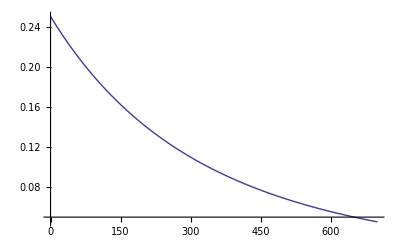

```mathematica
a1=1312
b1=7.41223261521925*^11
Plot[b1/(a1+x)^4,{x,0,700}]
```

```mathematica
So let's make these the values of a and b
```

```mathematica
a=1312
b=7.41223261521925*^11
```

1312

7.41223×10^11

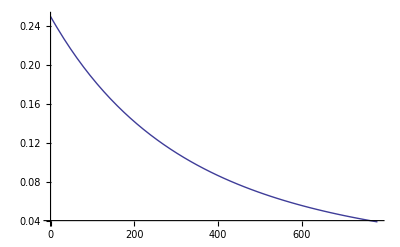

```mathematica
Plot[S[x],{x,0,780}]
```

{6.60644,6.3192,7.65139}

{0.863431,0.825889,1.}

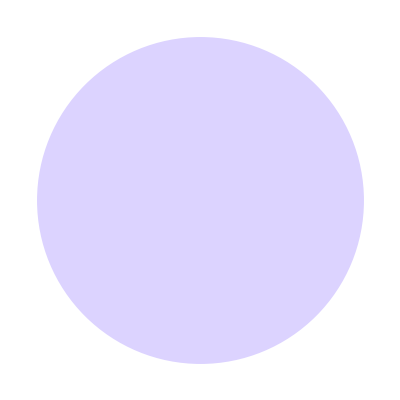

```mathematica
x=Sum[ S[l] xr[l],{l,380,780}];
y=Sum[ S[l] xg[l],{l,380,780}];
z=Sum[ S[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

```mathematica
This is if we assume all the light scattered comes into our eyes (but we're not correcting here)
```

```mathematica
With correction for human vision:
```

```mathematica
x=Sum[ S[l] 1/cr xr[l],{l,380,780}];
y=Sum[ S[l] 1/cg xg[l],{l,380,780}];
z=Sum[ S[l] 1/cb xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{705.952,675.249,817.475}

{0.863576,0.826018,1.}

-Graphics-

```mathematica
x=Sum[ S[l] cr xr[l],{l,380,780}];
y=Sum[ S[l] cg xg[l],{l,380,780}];
z=Sum[ S[l]cb xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{0.0618245,0.0591371,0.0716153}

{0.863286,0.825761,1.}

-Graphics-

{85.4777,-24.1816,236.305}

{0.361727,-0.102332,1.}

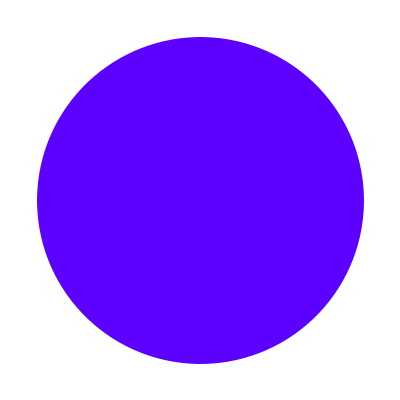

```mathematica
x=Sum[ S[l]/Sensitivity[l] xr[l],{l,380,780}];
y=Sum[ S[l]/Sensitivity[l] xg[l],{l,380,780}];
z=Sum[ S[l]/Sensitivity[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{153320.,164462.,193932.}

{0.790588,0.84804,1.}

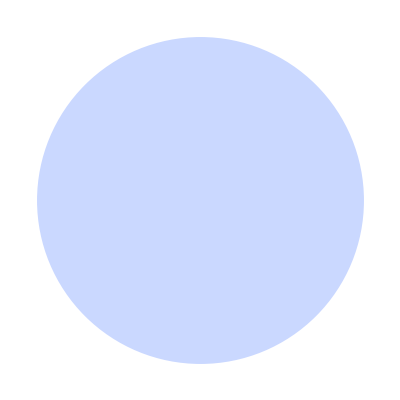

```mathematica
x=Sum[ sun[l]S[l] xr[l],{l,380,780}];
y=Sum[ sun[l] S[l]xg[l],{l,380,780}];
z=Sum[ sun[l] S[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

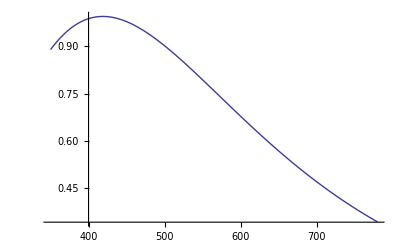

```mathematica
Plot[sun[l]S[l]/2000 ,{l,350,780},Axes->{True,False}]
```

```mathematica
Export["graph.png",Plot[sun[l]S[l]/2000 ,{l,350,780},Axes->{True,False}],Background->None]
```

graph.png

```mathematica
Plot[S[l]/0.09,{l,350,780},Axes->{True,False}]
```

```mathematica
Export["rayleigh.png",Plot[S[l]/0.09,{l,350,780},Axes->{True,False}],Background->None]
```

rayleigh.png

```mathematica
SystemOpen["rayleigh.png"]
```

{6.55407,6.37987,7.12804}

{0.919477,0.895039,1.}

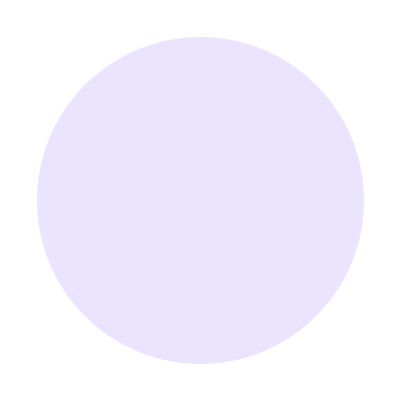

```mathematica
filter[l_]:=If[0<l<480, 1/480 l,1];
x=Sum[filter[l] S[l] xr[l],{l,380,780}];
y=Sum[ filter[l] S[l]xg[l],{l,380,780}];
z=Sum[ filter[l] S[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{151964.,165892.,180808.}

{0.840474,0.917505,1.}

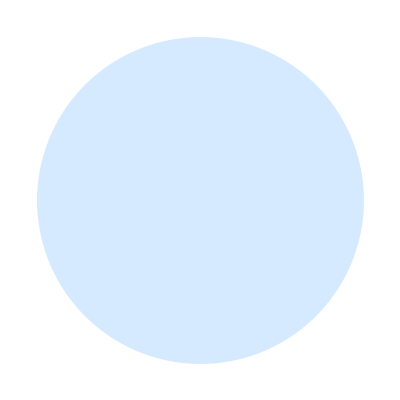

```mathematica
filter[l_]:=If[0<l<480, 1/480 l,1];
x=Sum[filter[l] sun[l]S[l] xr[l],{l,380,780}];
y=Sum[ filter[l]sun[l] S[l]xg[l],{l,380,780}];
z=Sum[ filter[l]sun[l] S[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

```mathematica
filter[l_]:=If[0<l<480, 1/480 l,1];
x=Sum[filter[l] S[l] xr[l],{l,380,780}];
y=Sum[ filter[l] S[l]xg[l],{l,380,780}];
z=Sum[ filter[l] S[l] xb[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{6.5513,6.37703,7.12468}

{0.919522,0.895062,1.}

-Graphics-

{1.84544×10^6,-526593.,5.69259×10^6}

{0.324182,-0.0925051,1.}

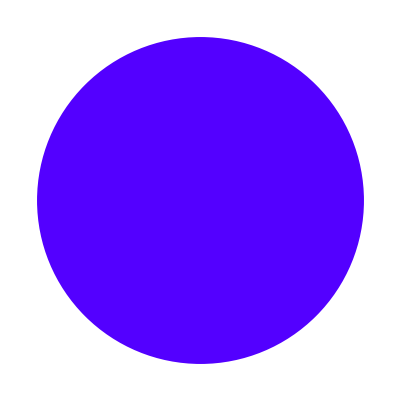

```mathematica
x=Sum[ sun[l]S[l] xr[l]/Sensitivity[l],{l,380,780}];
y=Sum[ sun[l] S[l]xg[l]/Sensitivity[l],{l,380,780}];
z=Sum[ sun[l] S[l] xb[l]/Sensitivity[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

```mathematica
x=Sum[ sun[l]S[l] xr[l],{l,380,780}];
y=Sum[ sun[l] S[l]xg[l],{l,380,780}];
z=Sum[ sun[l] S[l] xb[l] ,{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{153320.,164462.,193932.}

{0.790588,0.84804,1.}

-Graphics-

```mathematica
x=Sum[ S[l] xr[l] filter[l],{l,380,780}];
y=Sum[ S[l] xg[l] filter[l],{l,380,780}];
z=Sum[ S[l] xb[l] filter[l],{l,380,780}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{6.5513,6.37703,7.12468}

{0.919522,0.895062,1.}

-Graphics-

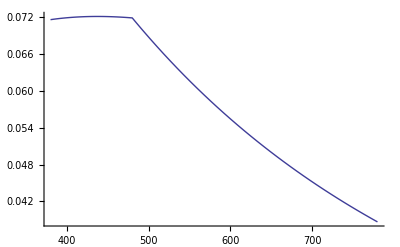

```mathematica
Plot[S[l] filter[l],{l,380,780}]
```

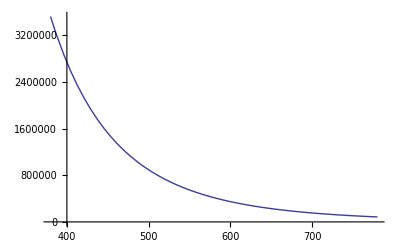

```mathematica
Plot[S[l] sun[l],{l,380,780}]
```

```mathematica
Clear[c,k]
```

```mathematica
sky[f_]:=(c/f^5) 1/(E^(k/f)-1)
```

```mathematica
Solve[{c/(525)^5 1/(E^(k/525)-1)==1},{c,k}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→39883798828125 (-1+ⅇ^(k/525))}}

```mathematica
k=30
c=39883798828125 (-1+ⅇ^(k/525))
```

30

39883798828125 (-1+ⅇ^(2/35))

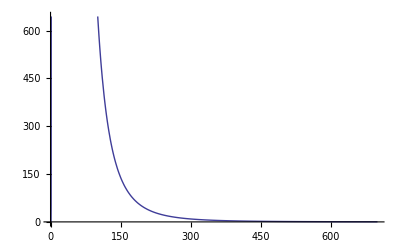

```mathematica
Plot[sky[f],{f,0,200}]
```

```mathematica
skyValues={
{360.52881355932203,135.49268359800863},
{380.84406779661015,186.28389830508513},
{401.1593220338983,540.6418690020732},
{421.47457627118644,895.3631751341186},
{441.78983050847455,1290.596382274991},
{462.1050847457627,1772.8484261119543},
{480.0762711864407,2684.285218116144},
{498.04745762711866,3649.67732222626},
{518.3627118644068,3656.5049492914704},
{538.6779661016949,3474.398150127173},
{558.9932203389831,3039.2282204458506},
{579.3084745762712,2456.180768696433},
{599.6237288135594,2080.779518081946},
{619.9389830508475,1754.4285512001202},
{640.2542372881356,1447.51603009383},
{660.5694915254237,1177.1187202107435},
{680.8847457627119,881.8329330262686},
{701.2,633.7807523991714},
{721.5152542372882,420.2454381024645},
{741.8305084745764,384.92615470109195},
{762.1457627118644,264.94971493149797},
{782.4610169491526,251.6122253510589},
{802.7762711864407,208.29956237843817},
{823.0915254237289,175.88696245751999},
{843.406779661017,174.17620679889706},
{863.7220338983052,165.9254133092527},
{884.0372881355934,162.21631275781692},
{897.320338983051,155.49399138649596}}
```

{{360.529,135.493},{380.844,186.284},{401.159,540.642},{421.475,895.363},{441.79,1290.6},{462.105,1772.85},{480.076,2684.29},{498.047,3649.68},{518.363,3656.5},{538.678,3474.4},{558.993,3039.23},{579.308,2456.18},{599.624,2080.78},{619.939,1754.43},{640.254,1447.52},{660.569,1177.12},{680.885,881.833},{701.2,633.781},{721.515,420.245},{741.831,384.926},{762.146,264.95},{782.461,251.612},{802.776,208.3},{823.092,175.887},{843.407,174.176},{863.722,165.925},{884.037,162.216},{897.32,155.494}}

```mathematica
sky=Interpolation[skyValues]
```

InterpolatingFunction[{{360.529,897.32}},<>]

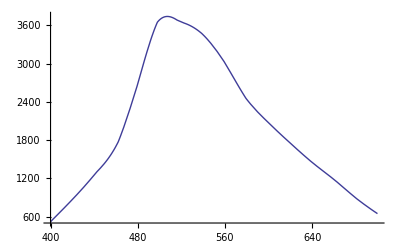

```mathematica
Plot[sky[l],{l,400,700}]
```

{0.170213,0.492048,0.25259}

{0.345929,1.,0.513345}

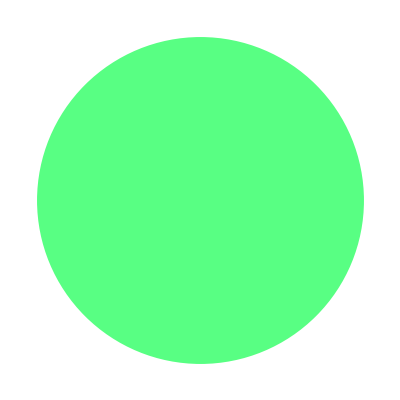

```mathematica
X=Sum[ sky[l]xr[l] S[l],{l,380,780}];
Y=Sum[ sky[l] xg[l] S[l],{l,380,780}];
Z=Sum[ sky[l] xb[l] S[l],{l,380,780}];
x=X/(X+Y+Z);
y=Y/(X+Y+Z);
z=Z/(X+Y+Z);
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

```mathematica
X=Sum[ sun[l]xr[l] S[l],{l,380,780}];
Y=Sum[ sun[l] xg[l] S[l],{l,380,780}];
Z=Sum[ sun[l] xb[l] S[l],{l,380,780}];
x=X/(X+Y+Z);
y=Y/(X+Y+Z);
z=Z/(X+Y+Z);
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{0.290316,0.31142,0.367233}

{0.790549,0.848017,1.}

-Graphics-

```mathematica
Sum
```

```mathematica
Rayleighdata={
{415.9773939985082,23.174823569912217},
{434.0180159504274,19.893281312754603},
{449.54730621378155,17.46640656377302},
{465.08520282288134,15.276493200986861},
{479.55247002122894,13.608583395490275},
{495.47420965058234,11.98714785701991},
{512.8538642492398,10.506971140053933},
{529.5157496127144,9.26421481438981},
{544.733490160078,8.259337885133974},
{561.4039818692983,7.2535429456652665},
{584.2469447472603,6.196454185552813},
{600.5645762809111,5.475242412071832},
{620.1526191978885,4.799357392850993},
{642.2829766481152,4.1218658557576475},
{657.5230936944174,3.7330885306098978}}
```

{{415.977,23.1748},{434.018,19.8933},{449.547,17.4664},{465.085,15.2765},{479.552,13.6086},{495.474,11.9871},{512.854,10.507},{529.516,9.26421},{544.733,8.25934},{561.404,7.25354},{584.247,6.19645},{600.565,5.47524},{620.153,4.79936},{642.283,4.12187},{657.523,3.73309}}

```mathematica
Ray=Interpolation[Rayleighdata]
```

InterpolatingFunction[{{415.977,657.523}},<>]

InterpolatingFunction::dmval: Input value {380.008} lies outside the range of data in the interpolating function. Extrapolation will be used.

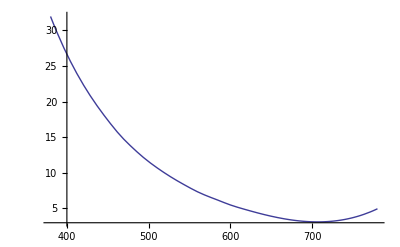

```mathematica
Plot[Ray[l],{l,380,780}]
```

```mathematica
Rayleigh scattering (done properly) + sun gives:
```

InterpolatingFunction::dmval: Input value {400} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {401} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {400} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {401} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {400} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {401} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {402} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{1.19522×10^7,2.14443×10^7,4.55177×10^7}

{0.262583,0.47112,1.}

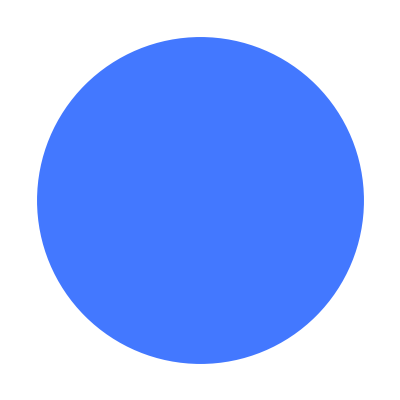

```mathematica
x=Sum[ Ray[l]xr[l] sun[l],{l,400,700}];
y=Sum[ Ray[l] xg[l] sun[l],{l,400,700}];
z=Sum[ Ray[l] xb[l] sun[l] ,{l,400,700}];
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

```mathematica
X=Sum[ sun[l] xr[l],{l,380,780}];
Y=Sum[ sun[l] xg[l],{l,380,780}];
Z=Sum[ sun[l] xb[l],{l,380,780}];
x=X/(X+Y+Z);
y=Y/(X+Y+Z);
z=Z/(X+Y+Z);
RGB.{x,y,z}
RGB.{x,y,z}/Max[RGB.{x,y,z}]
Graphics[{RGBColor[RGB.{x,y,z}/Max[RGB.{x,y,z}]],Disk[]}]
```

{0.373724,0.327613,0.306499}

{1.,0.876618,0.820122}

-Graphics-

```mathematica
X=680Sum[ sun[l] xr[l],{l,380,780,5}];
Y=680 Sum[ sun[l] xg[l],{l,380,780,5}];
Z=680 Sum[ sun[l] xb[l],{l,380,780,5}];
x=X/(X+Y+Z);
y=Y/(X+Y+Z);
z=Z/(X+Y+Z);
RGB.{x,y,z}
Graphics[{RGBColor[1/0.37371537470152233 RGB.{x,y,z}],Disk[]}]
```

{0.373715,0.327594,0.306522}

-Graphics-

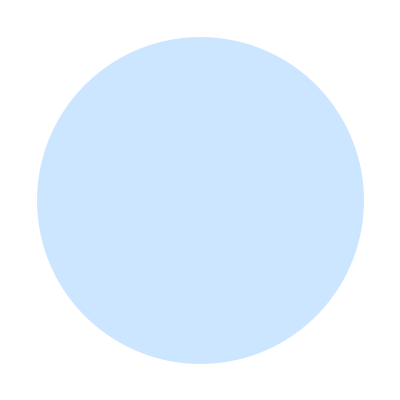

```mathematica
Graphics[{RGBColor[{.8,.9,1}],Disk[]}]
```